# Coca Cola Vs. Pepsi

Yifei Xiao
6/25/2019

People are consuming tons of soda everyday. From Coke to Pepsi, from Sprite to Mountain Dew. Most sparkling beverages we drink today are produced by two companies: Coca-Cola Company and PepsiCo. Both companies have been around for more than 100 years and sell billions of dollars of product annually. The war Pepsi and Coca Cola never ends. This article compares two companies in different aspects and some fun facts.

## 1. Revenue

When talking about a company, the first thing appears in our mind is how much money that company can earn each year. Coca Cola and Pepsi are no exceptions. We first collect raw data from a statistics website “macrotrends”.

```mathematica
ClearAll["Global`*"];
colaRevenueRaw = Import["https://www.macrotrends.net/stocks/charts/KO/coca-cola/revenue", "Data"];
pepsiRevenueRaw=Import["https://www.macrotrends.net/stocks/charts/PEP/pepsico/revenue", "Data"];
```

We are only interested in annual income of two companies, so we need to clean up other unrelated data such as quarterly revenue and so on. The annual income is in the level [[1,3,1,2]], which can be shown in the table form:

```mathematica
colaRevenue = colaRevenueRaw[[1,3,1]]//TableForm
pepsiRevenue = pepsiRevenueRaw[[1,3,1]]//TableForm
```

Coca-Cola Annual Revenue (Millions of US $) |  |  |  |  |  |  |  |  |  |  |  |  | 
2018
$31,856 | 2017
$35,410 | 2016
$41,863 | 2015
$44,294 | 2014
$45,998 | 2013
$46,854 | 2012
$48,017 | 2011
$46,542 | 2010
$35,119 | 2009
$30,990 | 2008
$31,944 | 2007
$28,857 | 2006
$24,088 | 2005
$23,104

Pepsico Annual Revenue (Millions of US $) |  |  |  |  |  |  |  |  |  |  |  |  | 
2018
$64,661 | 2017
$63,525 | 2016
$62,799 | 2015
$63,056 | 2014
$66,683 | 2013
$66,415 | 2012
$65,492 | 2011
$66,504 | 2010
$57,838 | 2009
$43,232 | 2008
$43,251 | 2007
$39,474 | 2006
$35,137 | 2005
$32,562

And we can use line plot to compare them more intuitively:

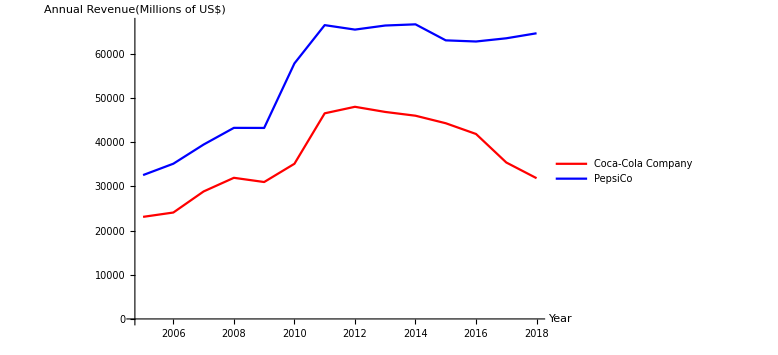

```mathematica
colaRevenue[[1,2,;;,2]]=ToExpression[StringDelete[#,{"$",","}]&/@colaRevenue[[1,2,;;,2]]];
pepsiRevenue[[1,2,;;,2]]=ToExpression[StringDelete[#,{"$",","}]&/@pepsiRevenue[[1,2,;;,2]]];
ListLinePlot[{colaRevenue[[1,2]],pepsiRevenue[[1,2]]},PlotLegends->{"Coca-Cola Company","PepsiCo"},PlotStyle->{Red,Blue},AxesLabel->{"Year","Annual Revenue(Millions of US$)"},ImageSize->Large]
```

PepsiCo earns more money than Coca-Cola Company and Coca-Cola company seems never win in this game. However, one thing we should keep in mind is that here we are comparing all products in each company. But when it comes to regular old cola, things change. We select data from “Brandz”, which takes top 100 most valuable global soft drinks brands 2018. Only top 10 beverage brands are selected in this article.

```mathematica
brandDataRaw = Import["https://www.statista.com/statistics/273063/leading-15-most-valuable-global-soft-drink-brands-based-on-brand-value/","Data"];
brandData = brandDataRaw[[2,1,2,1,1,2]][[1;;10]];
brandData[[;;,1]]=StringDelete[#,"*"]&/@brandData[[;;,1]];
brandData[[;;,2]]=ToExpression[StringDelete[#,","]&/@brandData[[;;,2]]];
PieChart[{brandData[[;;,2]]},ChartLabels->{brandData[[;;,1]]},ImageSize->Medium]
```

-Graphics-

As we can see, the brand value of Coca-Cola occupies the vast majority, whereas Pepsi cannot even win Diet Coke(another product by Coca-Cola Company). If we categorize these brands by their companies, we can see that Coca-Cola is still the overload of the soft drink market(KO means Coca-Cola company):

```mathematica
brandData[[;;,1]]=StringReplace[brandData[[;;,1]],{"Coca-Cola"->"KO","Red Bull"->"Others","Diet Coke"->"KO","Pepsi"->"PepsiCo","Lipton"->"PepsiCo","Nescafé"->"Others","Nespresso"->"Others","Fanta"->"KO","Tropicana"->"PepsiCo","Sprite"->"KO"}];
brandCat = List@@@Normal@Merge[Association/@Rule@@@brandData,Total]
brandLabel = ToString/@N[brandCat[[;;,2]]/Total[brandCat[[;;,2]]]*100,3];
brandLabel=Table[Style[StringJoin[brandLabel[[n]],"%"],Bold,16],{n,1,Length[brandLabel]}];
PieChart[brandCat[[;;,2]],ChartLabels->{brandLabel},ChartLegends->{brandCat[[;;,1]]},ChartStyle->{Red,Yellow,Blue}]
```

{{KO,91971},{Others,25010},{PepsiCo,24939}}

-Graphics-

## 2. Advertising Spending

Both companies spend billions of dollars promoting their potential and existing customers, both in US and around the world. But statistics shows that two companies have totally different marketing strategy. We use the same way as in section 1 to import data.

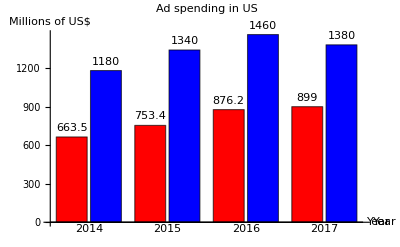
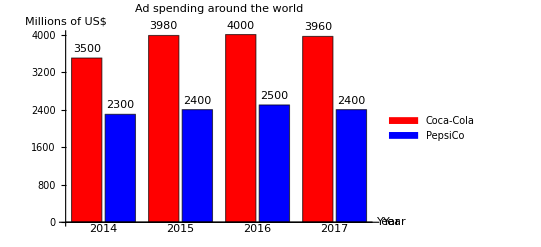

```mathematica
colaUSAdRaw=Import["https://www.statista.com/statistics/463084/coca-cola-ad-spend-usa/","Data"];
pepsiUSAdRaw= Import["https://www.statista.com/statistics/585833/pepsico-ad-spend-usa/","Data"];
colaUSAd = Sort[colaUSAdRaw[[2,1,2,1,1,2]][[1;;4]]];
pepsiUSAd= pepsiUSAdRaw[[2,1,2,1,1,2]];
pepsiUSAd[[;;,2]]=IntegerPart[pepsiUSAd[[;;,2]]*1000];
USadData = List@@@Normal@Merge[{Association/@Rule@@@colaUSAd,Association/@Rule@@@pepsiUSAd},Identity];
USadPlot = BarChart[USadData[[;;,2]],ChartStyle->{Red,Blue},ChartLabels->{{"2014","2015","2016","2017"},None},AxesLabel->{"Year","Millions of US$"},PlotLabel->Style[Framed["Ad spending in US"]],LabelingFunction->Above];

colaWorldAdRaw = Import["https://www.statista.com/statistics/286526/coca-cola-advertising-spending-worldwide/","Data"];
pepsiWorldAdRaw=Import["https://www.statista.com/statistics/286547/pepsico-advertising-spending-worldwide/","Data"];
colaWorldAd = Sort[colaWorldAdRaw[[2,1,2,1,1,2]][[2;;5]]];
colaWorldAd[[;;,2]]=IntegerPart[colaWorldAd[[;;,2]]*1000];
pepsiWorldAd = Sort[pepsiWorldAdRaw[[2,1,2,1,1,2]][[2;;5]]];
pepsiWorldAd[[;;,2]]=IntegerPart[pepsiWorldAd[[;;,2]]*1000];
WorldadData = List@@@Normal@Merge[{Association/@Rule@@@colaWorldAd,Association/@Rule@@@pepsiWorldAd},Identity];
WorldadPlot = BarChart[WorldadData[[;;,2]],ChartStyle->{Red,Blue},ChartLegends->{"Coca-Cola","PepsiCo"},ChartLabels->{{"2014","2015","2016","2017"},None},AxesLabel->{"Year","Millions of US$"},PlotLabel->Style[Framed["Ad spending around the world"]],LabelingFunction->Above];
Style[Row[{USadPlot,WorldadPlot}],ImageSizeMultipliers->{1.2,1.2}]
```

Coca-Cola company puts more emphasis all over the world whereas PepsiCo wants to occupy the US market.

## 3. Which one to choose?

Are you a “Cola guy” or “Pepsi guy”? Or you can enjoy both? How people around the world prefer? Data from “Google Trends” shows the search interest around the world. We import data from 2018 and focus on “Coca-Cola” and “Pepsi” search in “Drinking”:

```mathematica
pepsiMapData = Import["/Users/xiaoyifei/Downloads/Pepsi_map_data.csv"];
colaMapData = Import["/Users/xiaoyifei/Downloads/Cola_map_data.csv"];
pepsiMapData[[;;,1]]=SemanticInterpretation/@pepsiMapData[[;;,1]];
colaMapData[[;;,1]]=SemanticInterpretation/@colaMapData[[;;,1]];
pepsiMapData[[1]]
colaMapData[[1]]
pepsiMap = GeoRegionValuePlot[Rule@@@pepsiMapData,ImageSize->Full,PlotLabel->Style[Framed["World search interest in Pepsi around the world 2018"]]];
colaMap = GeoRegionValuePlot[Rule@@@colaMapData,ImageSize->Full,PlotLabel->Style[Framed["World search interest in Coca-Cola around the world 2018"]]];
TabView[{"Pepsi"->pepsiMap,"Cola"->colaMap}]
```

{Kazakhstan,100}

{Armenia,100}

12

People from North America except Mexico are more interested in Pepsi than Coca-Cola. Kazakhstan people are most interested in Pepsi whereas Armenia people are most interested in Coca-Cola.

## 4. Further explorations

The war between Coca-Cola Company and PepsiCo never ends, both two companies spend millions of dollars on data analysis to seize the market. Data in this article is published and open to everyone. Certainly there is more we don’t get access to. But one thing is certain, the more data, the more likely company will win the war.